Some random animations to start with

```mathematica
z=99/100;
Animate[Graphics[
  {Circle[{0,0},Sqrt[1-z^2+(z t)^2]],Circle[{0,0},z t]}
,PlotRange->{{-1,1},{-1,1}}],{t,0,1}]
```

```mathematica
Animate[Plot[
{Sqrt[1-z^2+(z t)^2-x^2],-Sqrt[1-z^2+(z t)^2-x^2],Sqrt[(z t)^2-x^2],-Sqrt[(z t)^2-x^2]}
,{x,-1,1},PlotRange->{Full,{-1,1}},PlotStyle->{Black}],{t,0,1}]
```

```mathematica
Animate[Plot3D[
{Sqrt[1-y^2+(y t)^2-x^2],-Sqrt[1-y^2+(y t)^2-x^2],Sqrt[(y t)^2-x^2],-Sqrt[(y t)^2-x^2]}
,{x,-1,1},{y,-1,1},PlotRange->{Full,Full,{-1,1}},BoxRatios->{1,1,1}],{t,0,1}]
```

A function that goes from 0 to 1 to 0, moving quickly through the middle stages

```mathematica
h=(-0.01+1.01 ⅇ^(1.02 (-4.5246279576875095+9.049255915375017 x)))/(1+ⅇ^(1.02 (-4.5246279576875095+9.049255915375017 x)));
```

```mathematica
tl=Join[{0,0,0,0,0},Table[h,{x,0,1,1/30}],{1,1,1,1,1},Table[h,{x,1,0,-1/30}]];
```

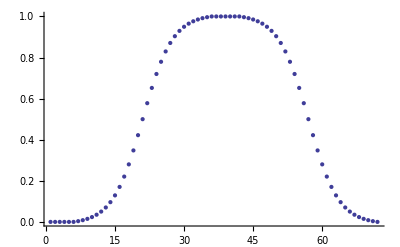

```mathematica
ListPlot[tl]
```

Here is the main animation:

```mathematica
T=Table[Plot3D[
{Sqrt[1-y^2+(y t)^2-x^2],-Sqrt[1-y^2+(y t)^2-x^2],Sqrt[(y t)^2-x^2],-Sqrt[(y t)^2-x^2]}
,{x,-1,1},{y,-1,1},PlotRange->{Full,Full,{-1,1}},BoxRatios->{1,1,1},PerformanceGoal->"Quality"],{t,tl}];
```

```mathematica
Export["cone sphere.gif",T]
```

cone sphere.gif

Here is a picture of one of the slides

```mathematica
T[[20]]
```

-Graphics3D-